Your Title Here

```mathematica
r=6.204;a=4*r;
```

```mathematica
f1[x_]=-√(r^2-x^2)+r;
```

```mathematica
f2[x_]=√(r^2-x^2)+r;
```

```mathematica
g1[x_]=-√(r^2-x^2-a^2+2*x*a)+r;
```

```mathematica
g2[x_]=√(r^2-x^2-a^2+2*x*a)+r;
```

```mathematica
Manipulate[
Module[{go,θ1,θ2,Psat,fW1,fW2,nWi,nN,nWfcalc,nWf,xW,xN,mWf,V1,V2,h1,h2},
go[1]=If[eq≤0.5,2*eq,1];go[2]=If[eq<0.5,0,eq-0.5];

θ1=ArcSin[(h1-r)/r];θ2=ArcSin[(h2-r)/r];

Psat[T_]:=100*10^(5.40221-1838.675/(T+241.263));
fW1=xW*Psat[T1];
fW2=Psat[22];

nWi=500/18.02;
nN=(2*mN/58.44); 

nWfcalc=w/.Quiet@Solve[fW2==Psat[T1]*w/(w+nN),w][[1]];
nWf=If[nWfcalc≥38.8457,38.8457,nWfcalc];

xW=nWi/(nWi+nN)+(nWf/(nWf+nN)-nWi/(nWi+nN))*go[2];
xN=1-xW;

mWf=If[xW<0.818,0,nWf*18.02];

V1=500*(1-go[2])+mWf*go[2];
V2=200+(500-mWf)*go[2];

h1=Hc/.Quiet@Solve[V1==π/3*Hc^2*(3*r-Hc),Hc,Reals][[2]];
h2=Hc/.Quiet@Solve[V2==π/3*Hc^2*(3*r-Hc),Hc,Reals][[2]];


Show[
Plot[{f1[x],f2[x]},{x,-r,r},PlotStyle->{{Thick,Black}},Filling->{1->h1},FillingStyle->Blend[{Cyan,Green},frac]],
Plot[{g1[x],g2[x]},{x,a-r,a+r},PlotStyle->{{Thick,Black}},Filling->{1->h2},FillingStyle->Blend[{Cyan,Green},1-frac]],
PlotRange->{{-r,a+r},{-0.6*r,3*r}},PlotRangePadding->Scaled@0.01,Axes->False,ImageSize->{600,450},
Epilog->{
{PointSize@0.01,Point@Table[{RandomReal[{a-0.65*r,a+0.65*r}],RandomReal[{0,0.15*r}]},{100}]},
{White,
FilledCurve[{Line[{r*Cos[#],r*Sin[#]+r}&/@Range[0,2*π,0.01]],Line[{2*r*Cos[#],2*r*Sin[#]+r}&/@Range[0,2*π,0.01]]}],
FilledCurve[{Line[{a+r*Cos[#],r*Sin[#]+r}&/@Range[0,2*π,0.01]],Line[{a+2*r*Cos[#],2*r*Sin[#]+r}&/@Range[0,2*π,0.01]]}]},
Thick,
BezierCurve[{{-r/5,2*r},{a/2,4*r},{a+r/5,2*r}}],BezierCurve[{{r/5,2*r},{a/2,3.5*r},{a-r/5,2*r}}],

Line[{{-r*Cos[θ1],h1},{r*Cos[θ1],h1}}],Line[{{a-r*Cos[θ2],h2},{a+r*Cos[θ2],h2}}],
{Circle[{#,r},r],
Thickness@0.0065,White,Circle[{#,r},r,{ArcCos[1/6],ArcCos[-1/6]}],
Thickness@0.015,GrayLevel@0.4,Circle[{#,r},r,{π/4*(1+go[1]),π/4*(3-go[1])}]}&/@{0,a}
}];{h1,h2}
],
Control[{{frac,0.7,"add to left"},0,1,0.1,Appearance->"Labeled"}],
Grid[{
{Control[{{eq,0,"go to equilibrium"},0,1.5,Trigger,AnimationRate->0.5}]},
{Style["conditions for left flask",Bold]},
{Control[{{T1,24,Row@{"temperature ",Subscript[Style["T",Italic],1]," (°C)"}},22.1,25.5,0.1,Appearance->"Labeled",ImageSize->Small}],SpanFromLeft,
Control[{{mN,15,"add grams of NaCl"},5,25,1,Appearance->"Labeled",ImageSize->Small}]}
},Alignment->Left],
SaveDefinitions->True]
```

```mathematica
Manipulate[
Module[{go,MWE,ρE,Psat,fW1,fW2,nWi,mN,nN,nWfcalc,nWf,xW,xN,mWf,V1,V2,h1,h2,θ1,θ2},
go[1]=If[eq≤0.5,2*eq,1];go[2]=If[eq<0.5,0,eq-0.5];
MWE=46.07;ρE=0.7893;

Psat[T_]:=100*10^(5.40221-1838.675/(T+241.263));
fW1=xW*Psat[T1];
fW2=Psat[22];

nWi=500/18.02;

mN=15;
nN=(2*mN/58.44); 

nWfcalc=w/.Quiet@Solve[fW2==Psat[T1]*w/(w+nN+nEtOH),w][[1]];
nWf=If[nWfcalc≥38.8457,38.8457,nWfcalc];

xW=nWi/(nWi+nN)+(nWf/(nWf+nN)-nWi/(nWi+nN))*go[2];
xN=1-xW;

mWf=If[xW<0.818,0,nWf*18.02];

(*V1=(500+nEtOH*MWE/ρE)*(1-go[2])+mWf*go[2];
V2=(200+(1-nEtOH)*MWE/ρE)+(500-mWf)*go[2];*)
V1=500*(1-go[2])+mWf*go[2];
V2=200+(500-mWf)*go[2];

h1=Hc/.Quiet@Solve[V1==π/3*Hc^2*(3*r-Hc),Hc,Reals][[2]];
h2=Hc/.Quiet@Solve[V2==π/3*Hc^2*(3*r-Hc),Hc,Reals][[2]];

θ1=ArcSin[(h1-r)/r];θ2=ArcSin[(h2-r)/r];

Show[
Plot[{f1[x],f2[x]},{x,-r,r},PlotStyle->{{Thick,Black}},Filling->{1->h1},FillingStyle->Blend[{Cyan,Green},nEtOH]],
Plot[{g1[x],g2[x]},{x,a-r,a+r},PlotStyle->{{Thick,Black}},Filling->{1->h2},FillingStyle->Blend[{Cyan,Green},1-nEtOH]],
PlotRange->{{-r,a+r},{-0.6*r,3.45*r}},PlotRangePadding->Scaled@0.01,Axes->False,ImageSize->{600,450},AspectRatio->0.7,
Epilog->{
{PointSize@0.01,Point@Table[{RandomReal[{a-0.65*r,a+0.65*r}],RandomReal[{0,0.15*r}]},{100}]},
{White,
FilledCurve[{Line[{r*Cos[#],r*Sin[#]+r}&/@Range[0,2*π,0.01]],Line[{2*r*Cos[#],2*r*Sin[#]+r}&/@Range[0,2*π,0.01]]}],
FilledCurve[{Line[{a+r*Cos[#],r*Sin[#]+r}&/@Range[0,2*π,0.01]],Line[{a+2*r*Cos[#],2*r*Sin[#]+r}&/@Range[0,2*π,0.01]]}]},
Thick,
BezierCurve[{{-r/5,2*r},{a/2,5*r},{a+r/5,2*r}}],BezierCurve[{{r/5,2*r},{a/2,4.5*r},{a-r/5,2*r}}],

Line[{{-r*Cos[θ1],h1},{r*Cos[θ1],h1}}],Line[{{a-r*Cos[θ2],h2},{a+r*Cos[θ2],h2}}],
{Circle[{#,r},r],
Thickness@0.0065,White,Circle[{#,r},r,{ArcCos[1/6],ArcCos[-1/6]}],
Thickness@0.015,GrayLevel@0.4,Circle[{#,r},r,{π/4*(1+go[1]),π/4*(3-go[1])}]}&/@{0,a},

(*{GrayLevel@0.5,Thickness@0.04,Line[{{-3.9,10.97},{-4.46,13.92}}],Thick,Line[{{-3.5,8.86},{-4.46,13.92}}]}*)
(*BezierCurve[{{r,1.25*r},{0.75*a/2,1.25*r},{0.75*a/2,1.75*r}}],BezierCurve[{{r,r},{0.9*a/2,r},{0.9*a/2,1.75*r}}],*)
(*BezierCurve[{{0.99*r,1.25*r},{0.65*a/2,1.25*r},{0.65*a/2,1.75*r}}],BezierCurve[{{r,r},{0.8*a/2,r},{0.8*a/2,1.75*r}}],
BezierCurve[{{a-0.99*r,1.25*r},{a-0.65*a/2,1.25*r},{a-0.65*a/2,1.75*r}}],BezierCurve[{{a-r,r},{a-0.8*a/2,r},{a-0.8*a/2,1.75*r}}]*)
}]
],
Grid[{
{Style["conditions for left flask",Bold],
Control[{{eq,0,"go to equilibrium"},0,1.5,Trigger}]},
{Control[{{T1,24,Row@{"temperature ",Subscript[Style["T",Italic],1]," (°C)"}},22.1,25.5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{nEtOH,0.4,"add moles of ethanol to left flask"},0,1,0.1,Appearance->"Labeled",ImageSize->Small}]}
},Alignment->Left],
SaveDefinitions->True]
```

```mathematica
Round[{{6.233615310501886,6.256759306923259},{6.600410440571078,6.217459828701559},{6.9672055706402745,6.256759306923259},{7.3340007007094705,6.37465774158836},{7.782305859682932,6.4925561762534585},{8.189856004204259,6.689053567361956},{8.556651134273455,6.88555095847045},{8.882691249890517,7.199946784244048},{9.086466322151182,7.5143426100176445},{9.412506437768243,7.9073373922346395},{9.57552649557677,8.37893113089503},{9.77930156783744,8.968423304220526},{9.77930156783744,9.24351965177242},{9.901566611193836,9.754412868654516},{9.901566611193836,10.068808694428109},{9.901566611193836,10.736899824197}},0.001]
```

{{6.234,6.257},{6.6,6.217},{6.967,6.257},{7.334,6.375},{7.782,6.493},{8.19,6.689},{8.557,6.886},{8.883,7.2},{9.086,7.514},{9.413,7.907},{9.576,8.379},{9.779,8.968},{9.779,9.244},{9.902,9.754},{9.902,10.069},{9.902,10.737}}

```mathematica
Manipulate[
Module[{p1,p2,p3,p4,y1,y2,y3,y4},
p1={{6.071,7.7},{6.519,7.75},{6.886,7.907},{7.13,8.025},{7.375,8.222},{7.538,8.458},{7.701,8.733},{7.823,9.047},{7.945,9.479},{7.986,9.872},(*{8.027,10.265},*){8.027,10.698}};

p2={{6.234,6.257},{6.6,6.217},{6.967,6.257},(*{7.334,6.375},*){7.782,6.493},{8.19,6.689},{8.557,6.886},(*{8.883,7.2},*){9.139,7.427},{9.413,7.907},{9.576,8.379},{9.779,9.244},{9.902,10.737}};

y1=Quiet@Interpolation[p1,InterpolationOrder->1];y2=Quiet@Interpolation[p2,InterpolationOrder->1];
(*y3=Quiet@Interpolation[p3];y4=Quiet@Interpolation[p4];*)

Show[
Plot[y1[x],{x,p1[[1,1]],p1[[-1,1]]}],
Plot[y2[x],{x,p2[[1,1]],p2[[-1,1]]},Filling->h],
Plot[h,{x,If[#<6,6,#]&@(z/.Quiet@FindRoot[y1[z]==h,{z,6}]),(z/.Quiet@FindRoot[y2[z]==h,{z,10}])},Filling->y2[x]],
(*Plot[{y2[x],Piecewise[{{h,(z/.Quiet@FindRoot[y1[z]==h,{z,6}])<x<(z/.Quiet@FindRoot[y2[z]==h,{z,10}])}}]},{x,p2[[1,1]],p2[[-1,1]]},Filling->{2->{1}}],*)
PlotRange->All,PlotRangePadding->Scaled@0.05(*,Epilog->{PointSize@0.02,Point@p1,Point@p2}*)]

(**)
],
Control[{{h,10},6.23,10}]
]
```

```mathematica
Module[{pt,m,b,y},
pt={{-3.9,10.97},{-4.46,13.92}};
m=(pt[[2,2]]-pt[[1,2]])/(pt[[2,1]]-pt[[1,1]]);

b=β/.Solve[pt[[1,2]]==m*pt[[1,1]]+β,β][[1]];
y[x_]:=m*x+b;
{#,y[#]}&@(-3.5)
]
```

{-3.5,8.86286}

```mathematica
Manipulate[
Plot[{
BezierFunction[{{0.99*r,1.25*r},{0.65*a/2,1.25*r},{0.65*a/2,1.75*r}}][t][[-1]],
BezierFunction[{{r,r},{0.8*a/2,r},{0.8*a/2,1.75*r}}][t][[-1]],
h
},{t,0,1},Filling->{3->{2}}],
Control[{{h,10},1,10}]
]
```

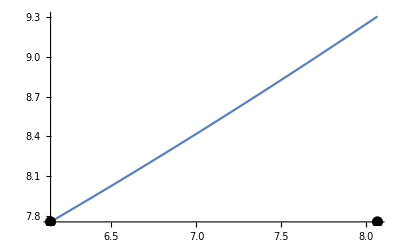

```mathematica
Module[{pt1},
pt1={{0.99*r,1.25*r},{0.65*a/2,1.25*r},{0.65*a/2,1.75*r}};

Plot[Fit[pt1,{1,x,x^2},x]/.x->z,{z,pt1[[1,1]],pt1[[-1,1]]},Epilog->{PointSize@0.02,Point@pt1},PlotRange->All]
]
```





```mathematica
Manipulate[
Module[{go,MWE,ρE,Psat,fW1,fW2,nWi,mN,nN,nWfcalc,nWf,xW,xN,mWf,V1,V2,h1,h2,θ1,θ2},
go[1]=If[eq≤0.5,2*eq,1];go[2]=If[eq<0.5,0,eq-0.5];
MWE=46.07;ρE=0.7893;

Psat[T_]:=100*10^(5.40221-1838.675/(T+241.263));
fW1=xW*Psat[T1];
fW2=Psat[22];

nWi=500/18.02;

mN=15;
nN=(2*mN/58.44); 

nWfcalc=w/.Quiet@Solve[fW2==Psat[T1]*w/(w+nN+nEtOH),w][[1]];
nWf=If[nWfcalc≥38.8457,38.8457,nWfcalc];

xW=nWi/(nWi+nN)+(nWf/(nWf+nN)-nWi/(nWi+nN))*go[2];
xN=1-xW;

mWf=If[xW<0.818,0,nWf*18.02]

],
Grid[{
{Style["conditions for left flask",Bold],
Control[{{eq,0,"go to equilibrium"},0,1.5,Trigger}]},
{Control[{{T1,24,Row@{"temperature ",Subscript[Style["T",Italic],1]," (°C)"}},22.1,25.5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{nEtOH,0.4,"add moles of ethanol to left flask"},0,1,0.1,Appearance->"Labeled",ImageSize->Small}]}
},Alignment->Left],
SaveDefinitions->True]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX